```mathematica
d = Import["/usr/local/google/home/aizatsky/projects/iflam/build/render.h5", {"Datasets", "d"}];
r = 
Import["/usr/local/google/home/aizatsky/projects/iflam/build/render.h5", {"Datasets", "r"}];
g = Import["/usr/local/google/home/aizatsky/projects/iflam/build/render.h5", {"Datasets", "g"}];
```

```mathematica
b = Import["/usr/local/google/home/aizatsky/projects/iflam/build/render.h5", {"Datasets", "b"}];
```

```mathematica
{Dimensions[d],
Dimensions[r],
Dimensions[g],
Dimensions[b]}
```

{{1024,768},{1024,768},{1024,768},{1024,768}}

```mathematica
Image[d]
```

-Graphics-

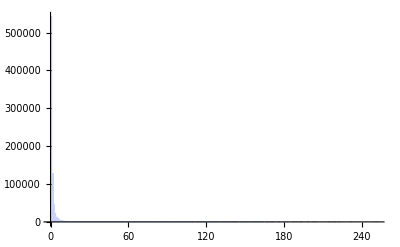

```mathematica
Histogram[Flatten[d]]
```

```mathematica
Image[r]
```

-Graphics-

```mathematica
Image[g]
```

-Graphics-

```mathematica
Image[b]
```

-Graphics-

```mathematica
Image[MapThread[Thread[{#1, #2, #3}]&, {r, g, b}]]
```

-Graphics-